# Reproduce Figure 1 of Wilkes (QJMAM, 1965)

ν is the axial wave number. We focus on the axially symmetric modes
Prepared by Yibin Fu (y.fu@keele.ac.uk) for the advanced summer schools 2022 at CISM

## The primary deformation

```mathematica
(* 1=θ, 2=z, 3=r *)
```

```mathematica
b0=1; a0=1/2; (*a0 and b0 are the undeformed inner and outer radii *)
```

```mathematica
F={{1/√λ,0,0},{0,λ,0},{0,0,1/√λ}}; Id={{1,0,0},{0,1,0},{0,0,1}};
Bt=F.Transpose[F]; σ= Bt-p Id;
pbar=p/.Solve[σ[[3,3]]==0,p][[1]]
```

1/λ

```mathematica
delta[i_,j_]:=If[i==j,1,0];
```

```mathematica
A1[j_,i_,l_,k_]:=delta[i,k] Bt[[j,l]];  (* instantaneous moduli, valid for the neo-Hookan model *)
```

## Derivation of the governing equations

```mathematica
u[r_,z_]=1/r D[ϕ[r, z],z]; v[r_,z_]=-1/r D[ϕ[r, z],r];  (* to satisfy incompressiblity automatically, ϕ=stream function *)
```

```mathematica
(* η below is grad u, with u denoting the incremental displacement field *)
```

```mathematica
η[1,1]=u[r,z]/r;η[1,2]=0;η[1,3]=0;η[2,1]=0;  (* 1=θ, 2=z, 3=r *)
η[2,2]=  D[v[r,z],z];
η[2,3]=D[v[r,z],r];
η[3,1]=0;
η[3,2]= D[u[r,z],z];
η[3,3]=D[u[r,z],r];
```

```mathematica
check=Tr[Table[η[i,j],{i,1,3},{j,1,3}]]  (* imcompressiblity given by tr(grad u)=0 *)
```

0

#### Incremental stress

```mathematica
χ[i_,j_]:=Sum[(A1[j,i,l,k])*η[k,l],{l,1,3},{k,1,3}]+pbar*η[j,i]-pstar[r,z]*delta[j,i]; (* χ=incremental stress *)
equilibrium1= D[χ[3,2],z]+D[χ[3,3],r]+1/r(χ[3,3]-χ[1,1]);(*Subscript[χ, 32,2]+Subscript[χ, 33,3]+1/r(Subscript[χ, 33]-Subscript[χ, 11])=0, equilibrium in the r-direction *)  
equilibrium2= D[χ[2,2],z]+  D[χ[2,3],r]+1/r  χ[2,3](*Subscript[χ, 22,2]+Subscript[χ, 23,3]+1/r Subscript[χ, 23]=0, equilibrium in the z-direction *);
```

```mathematica
BB1=χ[2,3]; (* zero shear in the z-direction on r=a, b *)
BB2=χ[3,3];(* zero normal stress on r=a, b*)
```

```mathematica
(*BB2 contains pstar[r,z]. To eliminate it, we differentiate BB2 w.r.t. z and then eliminate pstar^(0,1)[r,z] using equilibrium2=0 *)
```

```mathematica
BB2=D[BB2,z]/.Solve[equilibrium2==0,Derivative[0,1][pstar][r,z]][[1]]
```

(2 (-(ϕ^(0,2)[r,z])/r^2+(ϕ^(1,2)[r,z])/r))/λ-(-ϕ^(1,0)[r,z]-r^2 λ^3 ϕ^(1,2)[r,z]+r ϕ^(2,0)[r,z]-r^2 ϕ^(3,0)[r,z])/(r^3 λ)

```mathematica
eqn1=Simplify[D[equilibrium1, z]-D[equilibrium2, r]]  (*eliminating pstar[r,z] from the two equilibrium equations*)
```

(r^3 λ^3 ϕ^(0,4)[r,z]-3 ϕ^(1,0)[r,z]+r (-r (1+λ^3) ϕ^(1,2)[r,z]+3 ϕ^(2,0)[r,z]+r (r (1+λ^3) ϕ^(2,2)[r,z]-2 ϕ^(3,0)[r,z]+r ϕ^(4,0)[r,z])))/(r^4 λ)

```mathematica
ϕ[r_, z_]=r Φ[r] Exp[I ν z];
```

```mathematica
eqn1a=Coefficient[Simplify[eqn1],Exp[I ν z]]
```

((-3+r^2 (1+λ^3) ν^2+r^4 λ^3 ν^4) Φ[r]-r ((-3+r^2 (1+λ^3) ν^2) Φ'[r]+r ((3+r^2 (1+λ^3) ν^2) Φ''[r]-r (2 Φ^(3)[r]+r Φ^(4)[r]))))/(r^4 λ)

```mathematica
Φd4=Derivative[4][Φ][r]/.Solve[eqn1a==0,Derivative[4][Φ][r]][[1]]
```

(3 Φ[r]-r^2 ν^2 Φ[r]-r^2 λ^3 ν^2 Φ[r]-r^4 λ^3 ν^4 Φ[r]-3 r Φ'[r]+r^3 ν^2 Φ'[r]+r^3 λ^3 ν^2 Φ'[r]+3 r^2 Φ''[r]+r^4 ν^2 Φ''[r]+r^4 λ^3 ν^2 Φ''[r]-2 r^3 Φ^(3)[r])/r^4

```mathematica
BC1=Coefficient[Simplify[BB1],Exp[I ν z]]
```

-((-1+r^2 ν^2) Φ[r]+r (Φ'[r]+r Φ''[r]))/(r^2 λ)

```mathematica
BC2=Coefficient[Simplify[ BB2],Exp[I ν z]]
```

-((-1+r^2 λ^3 ν^2) Φ[r]+r ((1+r^2 (2+λ^3) ν^2) Φ'[r]-r (2 Φ''[r]+r Φ^(3)[r])))/(r^3 λ)

```mathematica
(* We assume in the two boundary conditions, Φ''[r] and Φ^(3)[r] are arbitrary, and Φ[r] and Φ'[r] are selected to stastify the two BCs *)
```

```mathematica
subBC=Simplify[Solve[{BC1==0, BC2==0},{Φ''[r],Derivative[3][Φ][r]}] ][[1]]
```

{Φ''[r]→(Φ[r]-r^2 ν^2 Φ[r]-r Φ'[r])/r^2,Φ^(3)[r]→((-3+r^2 (2+λ^3) ν^2) Φ[r]+r (3+r^2 (2+λ^3) ν^2) Φ'[r])/r^3}

```mathematica
yy1a={Φ[r], Φ'[r], Φ''[r], Derivative[3][Φ][r]}/.subBC/.{Φ[r]->1,Φ'[r]->0}/.r->a  (* one initial condition at r=a *)
```

{1,0,(1-a^2 ν^2)/a^2,(-3+a^2 (2+λ^3) ν^2)/a^3}

```mathematica
yy2a=Simplify[{Φ[r], Φ'[r], Φ''[r], Derivative[3][Φ][r]}/.subBC/.{Φ[r]->0,Φ'[r]->1}/.r->a] (* second initial condition at r=a *)
```

{0,1,-1/a,3/a^2+(2+λ^3) ν^2}

```mathematica
yy1b=yy1a/.a->b;yy2b=yy2a/.a->b;
```

```mathematica
check=Simplify[{Coefficient[BC1, {Φ[r],Φ'[r],Φ''[r],Derivative[3][Φ][r] }],Coefficient[BC2, {Φ[r],Φ'[r],Φ''[r],Derivative[3][Φ][r] }]}.Transpose[{yy1a,yy2a}]/.r->a]
```

{{0,0},{0,0}}

```mathematica
rightBC1=Coefficient[BC1,{Φ[r],Φ'[r],Φ''[r],Derivative[3][Φ][r] }]
```

{-(-1+r^2 ν^2)/(r^2 λ),-1/(r λ),-1/λ,0}

```mathematica
rightBC2=Coefficient[BC2,{Φ[r],Φ'[r],Φ''[r],Derivative[3][Φ][r] }]
```

{-(-1+r^2 λ^3 ν^2)/(r^3 λ),-(r+2 r^3 ν^2+r^3 λ^3 ν^2)/(r^3 λ),2/(r λ),1/λ}

```mathematica
MB={rightBC1,rightBC2}/.r->b
```

{{-(-1+b^2 ν^2)/(b^2 λ),-1/(b λ),-1/λ,0},{-(-1+b^2 λ^3 ν^2)/(b^3 λ),-(b+2 b^3 ν^2+b^3 λ^3 ν^2)/(b^3 λ),2/(b λ),1/λ}}

```mathematica
matrixA={{0,1,0,0},{0,0,1,0},{0,0,0,1},Coefficient[Φd4,{Φ[r],Φ'[r],Φ''[r],Derivative[3][Φ][r] }]};
```

## The determinant and compound matrix methods

We use the notation yy={y[1],y[2],y[3],y[4]}={Φ[r],Φ'[r],Φ''[r],Φ^(3)[r] };
The bcs at r=a has two independent solutions given by yy=yy1a and yy=yy2a.
Using each as initial condition to integrate from r=a to b, we obtain two independent solutions, yy^(1) and yy^(2), say. A genera solutions is given by y=c_1 yy^(1)+c_2yy^(2)=[yy^(1), yy^(2)] c
The bcs at r=b  are MB yy(b)=0, which may be written in the matrix form
MB  [yy^(1), yy^(2)] c =0. It then follows that det[MB  [yy^(1), yy^(2)]]=0

#### Determinant method

```mathematica
err1[λ0_]:=Module[{},λ=λ0; a=a0/√λ;b=b0/√λ;  AA0=matrixA;
sol1=NDSolve[{yy'[r]-AA0.yy[r]==0,yy[a]==yy1a},yy,{r,a,b}];
yyr1=yy[b]/.sol1;
sol2=NDSolve[{yy'[r]-AA0.yy[r]==0,yy[a]==yy2a},yy,{r,a,b}];
yyr2=yy[b]/.sol2;bbcc=MB.Transpose[Join[yyr1,yyr2]];
N1=Det[bbcc]
]
```

```mathematica
ind={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}};
```

#### Compound matrix method

```mathematica
err2[λ0_]:=Module[{},λ=λ0; a=a0/√λ;b=b0/√λ; d=(a+b)/2; AA0=matrixA;
BCa=Transpose[{yy1a,yy2a}];BCb=Transpose[{yy1b,yy2b}];
Do[i=ind[[p,1]];j=ind[[p,2]];
 ϕa[p]=Det[{BCa[[i]],BCa[[j]]}];
ϕb[p]=Det[{BCb[[i]],BCb[[j]]}],{p,1,6}];
ϕϕa={ϕa[1],ϕa[2],ϕa[3],ϕa[4],ϕa[5],ϕa[6]};
ϕϕb={ϕb[1],ϕb[2],ϕb[3],ϕb[4],ϕb[5],ϕb[6]};

mf0=Array[f0,{6,6}];Do[f0[p,q]=0,
{p,1,6},{q,1,6}];
mf0[[1,1]]=AA0[[1,1]]+AA0[[2,2]];
mf0[[2,2]]=AA0[[1,1]]+AA0[[3,3]];
mf0[[3,3]]=AA0[[1,1]]+AA0[[4,4]];
mf0[[4,4]]=AA0[[2,2]]+AA0[[3,3]];
mf0[[5,5]]=AA0[[2,2]]+AA0[[4,4]];
mf0[[6,6]]=AA0[[3,3]]+AA0[[4,4]];
mf0[[1,2]]=AA0[[2,3]];
mf0[[1,3]]=AA0[[2,4]];
mf0[[1,4]]=-AA0[[1,3]];
mf0[[1,5]]=-AA0[[1,4]];
mf0[[2,1]]=AA0[[3,2]];
mf0[[2,3]]=AA0[[3,4]];
mf0[[2,4]]=AA0[[1,2]];
mf0[[2,6]]=-AA0[[1,4]];
mf0[[3,1]]=AA0[[4,2]];
mf0[[3,2]]=AA0[[4,3]];
mf0[[3,5]]=AA0[[1,2]];
mf0[[3,6]]=AA0[[1,3]];
mf0[[4,1]]=-AA0[[3,1]];
mf0[[4,2]]=AA0[[2,1]];
mf0[[4,5]]=AA0[[3,4]];
mf0[[4,6]]=-AA0[[2,4]];
mf0[[5,1]]=-AA0[[4,1]];
     mf0[[5,3]]=AA0[[2,1]];
mf0[[5,4]]=AA0[[4,3]];
mf0[[5,6]]=AA0[[2,3]];
mf0[[6,2]]=-AA0[[4,1]];
mf0[[6,3]]=AA0[[3,1]];
mf0[[6,4]]=-AA0[[4,2]];
mf0[[6,5]]=AA0[[3,2]];
(* The following commented out Do loop computes the above matrix mf0 *)
(*Do[i=ind[[p,1]];j=ind[[p,2]];ii=ind[[q,1]];jj=ind[[q,2]]; If[(i==ii)&&(j==jj),mf0[[p,q]]=AA0[[i,i]]+AA0[[j,j]]];If[(i==ii)&&(j≠jj),mf0[[p,q]]=AA0[[j,jj]]];If[(j==jj)&&(i≠ii),mf0[[p,q]]=AA0[[i,ii]]];If[(j==ii)&&(i!=jj),mf0[[p,q]]=-AA0[[i,jj]]];
If[(i==jj)&&(j≠ii),mf0[[p,q]]=-AA0[[j,ii]]];
If[(i≠ii)&&(j≠ii)&&(i≠jj)&&(j≠jj),mf0[[p,q]]=0],
{p,1,6},{q,1,6}];*)
sol1=NDSolve[{ϕϕ'[r]-mf0.ϕϕ[r]==0,ϕϕ[a]==ϕϕa},ϕϕ,{r,a,b},WorkingPrecision->MachinePrecision][[1]];
ϕϕLeft=ϕϕ[d]/.sol1;
sol2=NDSolve[{ϕϕ'[r]-mf0.ϕϕ[r]==0,ϕϕ[b]==ϕϕb},ϕϕ,{r,a,b},WorkingPrecision->MachinePrecision][[1]];
ϕϕRight=ϕϕ[d]/.sol2;
N1=ϕϕLeft[[1]]*ϕϕRight[[6]]-ϕϕLeft[[2]]*ϕϕRight[[5]]+ϕϕLeft[[3]]*ϕϕRight[[4]]+ϕϕLeft[[4]]*ϕϕRight[[3]]-ϕϕLeft[[5]]*ϕϕRight[[2]]+ϕϕLeft[[6]]*ϕϕRight[[1]]
]
```

```mathematica
err[λ0_]:=err2[λ0];  (*select which method to use, determinant or compound matrix *)
```

Let’s  starts from wavenumber=0.35

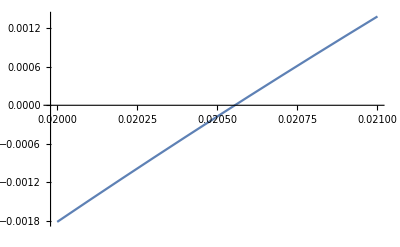

```mathematica
ν=0.35;data=Table[{t,err[t]},{t,0.02,0.021,0.0001}]; ListPlot[data,Joined->True, PlotRange->All]
```

```mathematica
froot[s0_, s1_]:=Module[{u0,u1, v0,v1},u0=s0; u1=s1; v0=err[u0]; v1=err[u1];Do[u2=(u1 v0-u0 v1)/(v0-v1);u0=u1;v0=v1;u1=u2;v1=err[u1]; (* Print["k=",k, "  ","error=", v1, "  ", Abs[1-u1/u0]];*)If[k==100, Print["No solution found"]];If[Abs[v1]<10^(-6)||Abs[1-u1/u0]<10^(-5), Break[]],{k,1,100}]; u1];
```

```mathematica
λinitial=froot[0.016,0.018]
```

0.0205546

```mathematica
data={{0.35,λinitial}};factor=1.001;
```

```mathematica
data
```

{{0.35,0.0205546}}

```mathematica
Do[ν=0.35+0.1*k; λnew=froot[λinitial,λinitial*factor];factor=If[λnew>λinitial, 1.01,0.995];λinitial=λnew; data=Append[data,{ν,λnew}],{k,1,200}]
```

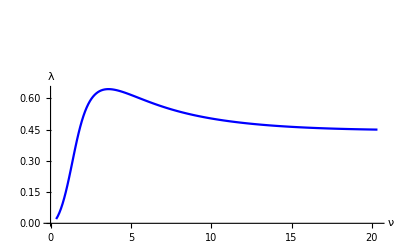

```mathematica
fig7a=ListPlot[{data},Joined->True,PlotStyle->{{PointSize[0.015], Blue},{PointSize[0.015], Black, Dashed}}, AxesStyle->{Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.005],Arrowheads[{0,0.05}]]},AxesLabel->{Style["ν",FontSize->20,FontFamily->"Times New Roman"],Style["λ",FontSize->20,FontFamily->"Times New Roman"]},Epilog->{Text[Style[ "Gent model",Medium],{4,2}]}]
```

## Closed-form solution

```mathematica
Clear[ν,λ]
```

```mathematica
b0=1; a0=1/2; (*a0 and b0 are the undeformed inner and outer radii, contrary to Wilkes' definition *)
```

```mathematica
eqn=Derivative[4][Φ][r]-1/r^4(3 Φ[r]-r^2 ν^2 Φ[r]-r^2 λ^3 ν^2 Φ[r]-r^4 λ^3 ν^4 Φ[r]-3 r Φ'[r]+r^3 ν^2 Φ'[r]+r^3 λ^3 ν^2 Φ'[r]+3 r^2 Φ''[r]+r^4 ν^2 Φ''[r]+r^4 λ^3 ν^2 Φ''[r]-2 r^3 Derivative[3][Φ][r]);
BC1=-((-1+r^2 ν^2) Φ[r]+r (Φ'[r]+r Φ''[r]))/(r^2 λ); BC2=-((-1+r^2 λ^3 ν^2) Φ[r]+r ((1+r^2 (2+λ^3) ν^2) Φ'[r]-r (2 Φ''[r]+r Derivative[3][Φ][r])))/(r^3 λ);
```

```mathematica
Simplify[Coefficient[eqn,{Derivative[3][Φ][r], Φ''[r], Φ'[r], Φ[r]}]]
```

{2/r,-3/r^2-(1+λ^3) ν^2,(3-r^2 (1+λ^3) ν^2)/r^3,-3/r^4+((1+λ^3) ν^2)/r^2+λ^3 ν^4}

```mathematica
tt1= Φ''[r]+1/r Φ'[r]-(1/r^2+ν^2)Φ[r];  (*tt1=0 is the modified Bessel's equation. It has solutions Subscript[I, ν][r]=Subscript[I, 1][ν r] and Subscript[K, ν][r]=Subscript[K, 1][ν r] *)
tt2= D[tt1,r,r]+1/r D[tt1,r]-(1/r^2+ν^2 λ^3 )tt1;
```

```mathematica
eqnguess=Derivative[4][Φ][r]/.Solve[tt2==0, Derivative[4][Φ][r]][[1]]
```

(3 Φ[r]-r^2 ν^2 Φ[r]-r^2 λ^3 ν^2 Φ[r]-r^4 λ^3 ν^4 Φ[r]-3 r Φ'[r]+r^3 ν^2 Φ'[r]+r^3 λ^3 ν^2 Φ'[r]+3 r^2 Φ''[r]+r^4 ν^2 Φ''[r]+r^4 λ^3 ν^2 Φ''[r]-2 r^3 Φ^(3)[r])/r^4

```mathematica
check=Simplify[eqn-(Derivative[4][Φ][r]-eqnguess)]
```

0

```mathematica
Φ[r_]=c1*BesselI[1, ν r λ^(3/2)]+c2* BesselI[1, ν r ]+c3*BesselK[1, ν r λ^(3/2)]+c4* BesselK[1, ν r ];
```

```mathematica
bc1a=Coefficient[BC1/.r->aa,{c1,c2,c3,c4}];
bc2a=Coefficient[BC2/.r->aa,{c1,c2,c3,c4}];
bc1b=Coefficient[BC1/.r->bb,{c1,c2,c3,c4}];
bc2b=Coefficient[BC2/.r->bb,{c1,c2,c3,c4}];
```

```mathematica
bif=Det[{bc1a,bc2a,bc1b,bc2b}]/.{aa->a0/√λ,bb->b0/√λ};
```

```mathematica
fig7a=ListPlot[{data},Joined->True,PlotStyle->{{PointSize[0.015], Blue},{PointSize[0.015], Black, Dashed}}, AxesStyle->{Directive[Black,Thickness[0.0055],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.005],Arrowheads[{0,0.05}]]},AxesLabel->{Style["ν",FontSize->20,FontFamily->"Times New Roman"],Style["λ",FontSize->20,FontFamily->"Times New Roman"]},Epilog->{Text[Style[ "Gent model",Medium],{4,2}]}]
```

-Graphics-

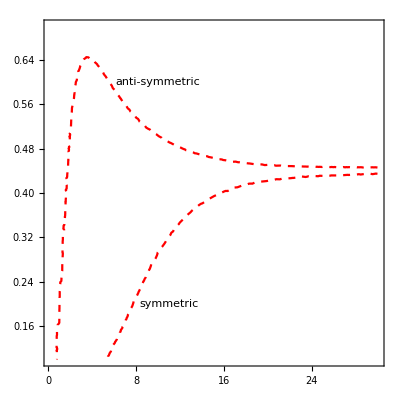

```mathematica
fig7b=ContourPlot[bif==0,{ν,0.2,30},{λ,0.1,0.7},ContourStyle->{{PointSize[0.015], Red, Dashed}} ,Epilog->{{Text[Style[ "anti-symmetric",Medium],{10,0.6}]},{Text[Style[ "symmetric",Medium],{11,0.2}]}}]
```

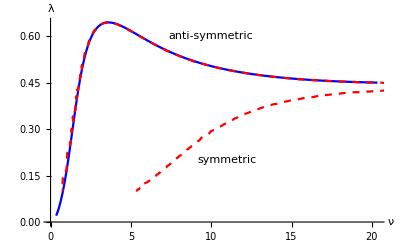

```mathematica
Show[fig7a,fig7b,Epilog->{{Text[Style[ "anti-symmetric",Medium],{10,0.6}]},{Text[Style[ "symmetric",Medium],{11,0.2}]}}]
```

```mathematica
dbif=D[bif,ν];  
(* differentiating bif[ν, λ(ν)] w.r.t. ν, we obtain D[bif,ν]+D[bif, λ] λ'(ν)=0. At the maximum of λ, we have λ'(ν)=0, and so  D[bif,ν] *)
```

```mathematica
submax=FindRoot[{bif==0,dbif==0},{ν,3.5},{λ,0.645}]
```

{ν→3.60521,λ→0.644629}

```mathematica
resultsave={ν->3.622767695476502,λ->0.6483800594600675};
```

Wilkes'(1955) horizontal axis is (a ν). Since his a is our b, this is (b v)=(b_0 ν/√λ)  in our notation.

The following is where the maximum is attained in Wilke’s notation

```mathematica
b0 ν/√λ/.submax
```

4.4903